```mathematica
γ[1]
```

```mathematica
CoeffiMat[n_]:= {
{r[n]^(m[1,n]-2),r[n]^(m[2,n]-2),r[n]^(m[3,n]-2),r[n]^(m[4,n]-2)}
,{g[1,n] r[n]^(m[1,n]-2),g[2,n] r[n]^(m[2,n]-2),g[3,n] r[n]^(m[3,n]-2),g[4,n] r[n]^(m[4,n]-2)}
,{r[n-1]^(m[1,n]-2),r[n-1]^(m[2,n]-2),r[n-1]^(m[3,n]-2),r[n-1]^(m[4,n]-2)}
,{g[1,n] r[n-1]^(m[1,n]-2),g[2,n]  r[n-1]^(m[2,n]-2),g[3,n] r[n-1]^(m[3,n]-2),g[4,n] r[n-1]^(m[4,n]-2)}}
μMat[n_]:={-μ[1,n],-μ[2,n],-μ[1,n],-μ[2,n]}
ΚMat[n_] := LinearSolve[CoeffiMat[n],μMat[n]]
```

```mathematica
r/@Range[0,3]
```

{1/500,3/500,1/100,7/500}

```mathematica
ClearAll[ΚMat]
```

```mathematica
CoeffiMat[3].ΚMat[3]-μMat[3]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.072205,6.05582,3.60513×10^8,4.29848×10^6},{-0.0835013,11.7593,-1.91805×10^8,3.44815×10^6},{0.0586943,6.97953,1.70374×10^9,1.43276×10^7},{-0.0678769,13.5529,-9.06447×10^8,1.14933×10^7}} may contain significant numerical errors.

{-9.53674×10^-7,1.07288×10^-6,-9.53674×10^-7,5.96046×10^-7}

```mathematica
ΚMat[1]
ΚMat[2]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0428552,8.65819,1.80049×10^10,8.91185×10^7},{-0.0495598,16.8126,-9.57922×10^9,7.14891×10^7},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}} may contain significant numerical errors.

{1.20071×10^11,3.15989×10^8,0.00178612,-0.937807}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0586943,6.97953,1.70374×10^9,1.43276×10^7},{-0.0678769,13.5529,-9.06447×10^8,1.14933×10^7},{0.0428552,8.65819,1.80049×10^10,8.91185×10^7},{-0.0495598,16.8126,-9.57922×10^9,7.14891×10^7}} may contain significant numerical errors.

{8.61973×10^10,4.10792×10^8,0.159084,-25.6389}

```mathematica
Κ[#,3]&/@Range[4]
```

{6.38809×10^10,5.16046×10^8,3.18221,-245.368}

```mathematica
μ[#,1]&/@Range[2]
```

{-0.783012,0.0722243}

```mathematica
m[#,1]&/@Range[4]
```

{2.6157,1.57809,-2.6157,-1.57809}

```mathematica
g[#,1]&/@Range[4]
```

{-1.15645,1.94181,-0.532033,0.80218}

```mathematica
EIofN/@Range[3]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.072205,6.05582,3.60513×10^8,4.29848×10^6},{-0.0835013,11.7593,-1.91805×10^8,3.44815×10^6},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{527.999,461.918,437.369}

```mathematica
EIofN/@Range[10]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.072205,6.05582,3.60513×10^8,4.29848×10^6},{-0.0835013,11.7593,-1.91805×10^8,3.44815×10^6},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{527.999,461.918,437.369,427.085,421.935,419.017,417.212,416.021,415.195,414.6}

```mathematica
EIofN/@Range[10]
```

{-1258.9,-14.2182,158.795,228.866,267.752,292.74,310.235,323.201,333.208,341.173}

```mathematica
EIofN/@Range[10]
```

{-1258.9,-14.2182,158.795,228.866,267.752,292.74,310.235,323.201,333.208,341.173}

```mathematica
p[n_]:= (g[1,n] (g[4,n] (m[2,n]-m[3,n]) (m[1,n]-m[4,n])-g[3,n] (m[1,n]-m[3,n]) (m[2,n]-m[4,n])+g[2,n] (m[1,n]-m[2,n]) (m[3,n]-m[4,n]))+g[2,n] g[3,n] (m[2,n]-m[3,n]) (m[1,n]-m[4,n])-g[2,n] g[4,n] (m[1,n]-m[3,n]) (m[2,n]-m[4,n])+g[3,n] g[4,n] (m[1,n]-m[2,n]) (m[3,n]-m[4,n]))
P[1,n_]:=1/p[n](g[3,n] g[4,n] (-2+m[2,n]) (m[3,n]-m[4,n]) μ[1,n]+g[2,n] (g[3,n] (m[2,n]-m[3,n]) (-2+m[4,n])+g[4,n] (-2+m[3,n]) (-m[2,n]+m[4,n])) μ[1,n]-g[3,n] (-2+m[3,n]) (m[2,n]-m[4,n]) μ[2,n]+g[2,n] (-2+m[2,n]) (m[3,n]-m[4,n]) μ[2,n]+g[4,n] (m[2,n]-m[3,n]) (-2+m[4,n]) μ[2,n])
P[2,n_]:=1/p[n](g[1,n] (g[4,n] (-2+m[3,n]) (m[1,n]-m[4,n])-g[3,n] (m[1,n]-m[3,n]) (-2+m[4,n])) μ[1,n]-g[3,n] g[4,n] (-2+m[1,n]) (m[3,n]-m[4,n]) μ[1,n]+g[3,n] (-2+m[3,n]) (m[1,n]-m[4,n]) μ[2,n]-g[1,n] (-2+m[1,n]) (m[3,n]-m[4,n]) μ[2,n]-g[4,n] (m[1,n]-m[3,n]) (-2+m[4,n]) μ[2,n])
P[3,n_]:=1/p[n](g[2,n] g[4,n] (-2+m[1,n]) (m[2,n]-m[4,n]) μ[1,n]+g[1,n] (g[2,n] (m[1,n]-m[2,n]) (-2+m[4,n])+g[4,n] (-2+m[2,n]) (-m[1,n]+m[4,n])) μ[1,n]-g[2,n] (-2+m[2,n]) (m[1,n]-m[4,n]) μ[2,n]+g[1,n] (-2+m[1,n]) (m[2,n]-m[4,n]) μ[2,n]+g[4,n] (m[1,n]-m[2,n]) (-2+m[4,n]) μ[2,n])
P[4,n_]:=1/p[n](g[1,n] (g[3,n] (-2+m[2,n]) (m[1,n]-m[3,n])-g[2,n] (m[1,n]-m[2,n]) (-2+m[3,n])) μ[1,n]-g[2,n] g[3,n] (-2+m[1,n]) (m[2,n]-m[3,n]) μ[1,n]+g[2,n] (-2+m[2,n]) (m[1,n]-m[3,n]) μ[2,n]-g[1,n] (-2+m[1,n]) (m[2,n]-m[3,n]) μ[2,n]-g[3,n] (m[1,n]-m[2,n]) (-2+m[3,n]) μ[2,n])
Κ[i_,n_]:=P[i,n] r[n]^(-m[i,n]+2)
```

```mathematica
Κ[#,1]&/@Range[4]
Κ[#,10]&/@Range[4]
```

{1.58497×10^11,2.76855×10^8,0.00350078,-1.24837}

{6.38809×10^10,5.16046×10^8,3.18221,-245.368}

```mathematica
Κ[i_,n_]:=P[i,n] r[n]^(-m[i,n]+2)
Κ[#,1]&/@Range[4]
Κ[#,10]&/@Range[4]
```

{1.58497×10^11,2.76855×10^8,0.00350078,-1.24837}

{6.38809×10^10,5.16046×10^8,3.18221,-245.368}

```mathematica
ΚMat[1]
ΚMat[1000]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0218695,13.7289,2.79029×10^12,4.44481×10^9},{-0.0252909,26.6589,-1.48453×10^12,3.56554×10^9},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}} may contain significant numerical errors.

{2.11298×10^11,2.27342×10^8,0.000405496,-0.234759}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.072205,6.05582,3.60513×10^8,4.29848×10^6},{-0.0835013,11.7593,-1.91805×10^8,3.44815×10^6},{0.0721669,6.05801,3.61942×10^8,4.31169×10^6},{-0.0834573,11.7635,-1.92565×10^8,3.45875×10^6}} may contain significant numerical errors.

{6.38977×10^10,5.15953×10^8,3.17592,-244.991}

```mathematica
Δr[10]//N
```

0.0012

```mathematica
CoeffiMat[n_]:= {
{r[n]^(m[1,n]-2),r[n]^(m[2,n]-2),r[n]^(m[3,n]-2),r[n]^(m[4,n]-2)}
,{g[1,n] r[n]^(m[1,n]-2),g[2,n] r[n]^(m[2,n]-2),g[3,n] r[n]^(m[3,n]-2),g[4,n] r[n]^(m[4,n]-2)}
,{r[n-1]^(m[1,n]-2),r[n-1]^(m[2,n]-2),r[n-1]^(m[3,n]-2),r[n-1]^(m[4,n]-2)}
,{g[1,n] r[n-1]^(m[1,n]-2),g[2,n]  r[n-1]^(m[2,n]-2),g[3,n] r[n-1]^(m[3,n]-2),g[4,n] r[n-1]^(m[4,n]-2)}}
μMat[n_]:={-μ[1,n],-μ[2,n],-μ[1,n],-μ[2,n]}
ΚMat[n_] := LinearSolve[CoeffiMat[n],μMat[n]]
```

```mathematica
Κ[i_,n_]:=ΚMat[n][[i]]
```

```mathematica
EI[Νl]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0218695,13.7289,2.79029×10^12,4.44481×10^9},{-0.0252909,26.6589,-1.48453×10^12,3.56554×10^9},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

412.012

```mathematica
CoeffiMat[1]
CoeffiMat[2]
```

{{0.0291015,11.2878,3.27706×10^11,8.4487×10^8},{-0.0336544,21.9188,-1.7435×10^11,6.77738×10^8},{0.0217891,13.7636,2.86841×10^12,4.54097×10^9},{-0.0251979,26.7262,-1.52609×10^12,3.64268×10^9}}

{{0.0354054,9.86866,7.53564×10^10,2.70353×10^8},{-0.0409445,19.1631,-4.00921×10^10,2.16872×10^8},{0.0291015,11.2878,3.27706×10^11,8.4487×10^8},{-0.0336544,21.9188,-1.7435×10^11,6.77738×10^8}}

```mathematica
EI[3]
```

0.147885

```mathematica
EIofN/@Range[10]
```

{-1258.9,-14.2182,158.795,228.866,267.752,292.74,310.235,323.201,333.208,341.173}

```mathematica
p[n_]:= g[1,n](g[3,n]-g[4,n])(m[1,n]-m[3,n])(m[2,n]-m[4,n])+g[2,n](g[3,n]-g[4,n])(m[2,n]-m[3,n])(m[4,n]-m[1,n])-(g[1,n] g[2,n]+g[3,n] g[4,n]-g[1,n] g[4,n] - g[2,n] g[4,n])(m[1,n]-m[2,n])(m[3,n]-m[4,n]);P[1,n_]:=-1/p[n]((g[2,n] g[3,n] (m[2,n]-m[3,n])(m[4,n]-2)+g[2,n] g[4,n] (m[4,n]-m[2,n])(m[3,n]-2)
+g[3,n] g[4,n] (m[3,n]-m[4,n])(m[2,n]-2))μ[1,n] +(g[2,n](m[3,n]-m[4,n])(m[2,n]-2)
+g[3,n](m[4,n]-m[2,n])(m[3,n]-2)+g[4,n](m[2,n]-m[3,n])(m[4,n]-2))μ[2,n]);
P[2,n_]:=
1/p[n]((g[1,n] g[3,n] (m[1,n]-m[3,n])(m[4,n]-2)+g[1,n] g[4,n] (m[4,n]-m[1,n])(m[3,n]-2)
+g[3,n] g[4,n] (m[3,n]-m[4,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[3,n]-m[4,n])(m[1,n]-2)
+g[3,n](m[4,n]-m[1,n])(m[3,n]-2)+g[4,n](m[1,n]-m[3,n])(m[4,n]-2))μ[2,n]);
P[3,n_]:=
-1/p[n]((g[1,n] g[2,n] (m[1,n]-m[2,n])(m[4,n]-2)+g[1,n] g[4,n] (m[4,n]-m[1,n])(m[2,n]-2)
+g[2,n] g[4,n] (m[2,n]-m[4,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[2,n]-m[4,n])(m[1,n]-2)
+g[2,n](m[4,n]-m[1,n])(m[2,n]-2)+g[4,n](m[1,n]-m[2,n])(m[4,n]-2))μ[2,n]);
P[4,n_]:=
1/p[n]((g[1,n] g[2,n] (m[1,n]-m[2,n])(m[3,n]-2)+g[1,n] g[3,n] (m[3,n]-m[1,n])(m[2,n]-2)
+g[2,n] g[3,n] (m[2,n]-m[3,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[2,n]-m[3,n])(m[1,n]-2)
+g[2,n](m[3,n]-m[1,n])(m[2,n]-2)+g[3,n](m[1,n]-m[2,n])(m[3,n]-2))μ[2,n]);
```

```mathematica
𝒞={{1.05*10^-10&,-0.0669*10^-10&,-0.08049999999999999*10^-10&,-0.0161*10^-10&,0.&,0.&},{-0.0669*10^-10&,1.3599999999999999*10^-10&,-0.45099999999999996*10^-10&,0.22599999999999998*10^-10&,0.&,0.&},{-0.08049999999999999*10^-10&,-0.45099999999999996*10^-10&,0.732*10^-10&,-0.974*10^-10&,0.&,0.&},{-0.0161*10^-10&,0.22599999999999998*10^-10&,-0.974*10^-10&,2.57*10^-10&,0.&,0.&},{0.&,0.&,0.&,0.&,4.55*10^-10&,0.958*10^-10&},
{0.&,0.&,0.&,0.&,0.958*10^-10&,2.95*10^-10&}
};
C1 =Table[N@ 𝒞[[i,j]]@1,{i,6},{j,6}]
```

{{1.05×10^-10,-6.69×10^-12,-8.05×10^-12,-1.61×10^-12,0.,0.},{-6.69×10^-12,1.36×10^-10,-4.51×10^-11,2.26×10^-11,0.,0.},{-8.05×10^-12,-4.51×10^-11,7.32×10^-11,-9.74×10^-11,0.,0.},{-1.61×10^-12,2.26×10^-11,-9.74×10^-11,2.57×10^-10,0.,0.},{0.,0.,0.,0.,4.55×10^-10,9.58×10^-11},{0.,0.,0.,0.,9.58×10^-11,2.95×10^-10}}

```mathematica
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
nφ[n_]:=25./180 π;
𝒞=Table[Evaluate[𝒞𝒻[nφ[#]][[m,n]]]&,{m,6},{n,6}];
```

```mathematica
C2=Table[N@ 𝒞[[i,j]]@1,{i,6},{j,6}]
```

{{1.05×10^-10,-6.69507×10^-12,-8.04493×10^-12,-1.60869×10^-12,0.,0.},{-6.69507×10^-12,1.36173×10^-10,-4.5086×10^-11,2.23352×10^-11,0.,0.},{-8.04493×10^-12,-4.5086×10^-11,7.31794×10^-11,-9.74076×10^-11,0.,0.},{-1.60869×10^-12,2.23352×10^-11,-9.74076×10^-11,2.57296×10^-10,0.,0.},{0.,0.,0.,0.,4.55348×10^-10,9.57556×10^-11},{0.,0.,0.,0.,9.57556×10^-11,2.94652×10^-10}}

```mathematica
C1-C2//Chop
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Round
```

```mathematica
C2
```

{{1.05×10^-10,-6.69507×10^-12,-8.04493×10^-12,-1.60869×10^-12,0.,0.},{-6.69507×10^-12,1.36173×10^-10,-4.5086×10^-11,2.23352×10^-11,0.,0.},{-8.04493×10^-12,-4.5086×10^-11,7.31794×10^-11,-9.74076×10^-11,0.,0.},{-1.60869×10^-12,2.23352×10^-11,-9.74076×10^-11,2.57296×10^-10,0.,0.},{0.,0.,0.,0.,4.55348×10^-10,9.57556×10^-11},{0.,0.,0.,0.,9.57556×10^-11,2.94652×10^-10}}

```mathematica
SetAccuracy[-6.695073009829135*^-12,16]
```

-6.695×10^-12

```mathematica
10^-6 CMat25//MatrixForm
```

(1.05×10^-10 | -6.69×10^-12 | -8.05×10^-12 | -1.61×10^-12 | 0. | 0.
-6.69×10^-12 | 1.36×10^-10 | -4.51×10^-11 | 2.26×10^-11 | 0. | 0.
-8.05×10^-12 | -4.51×10^-11 | 7.32×10^-11 | -9.74×10^-11 | 0. | 0.
-1.61×10^-12 | 2.26×10^-11 | -9.74×10^-11 | 2.57×10^-10 | 0. | 0.
0. | 0. | 0. | 0. | 4.55×10^-10 | 9.58×10^-11
0. | 0. | 0. | 0. | 9.58×10^-11 | 2.95×10^-10)

```mathematica
C2//MatrixForm
```

(1.05×10^-10 | -6.69507×10^-12 | -8.04493×10^-12 | -1.60869×10^-12 | 0. | 0.
-6.69507×10^-12 | 1.36173×10^-10 | -4.5086×10^-11 | 2.23352×10^-11 | 0. | 0.
-8.04493×10^-12 | -4.5086×10^-11 | 7.31794×10^-11 | -9.74076×10^-11 | 0. | 0.
-1.60869×10^-12 | 2.23352×10^-11 | -9.74076×10^-11 | 2.57296×10^-10 | 0. | 0.
0. | 0. | 0. | 0. | 4.55348×10^-10 | 9.57556×10^-11
0. | 0. | 0. | 0. | 9.57556×10^-11 | 2.94652×10^-10)

```mathematica
CMatString//MatrixForm
```

(C11 | C12 | C13 | C14 | 0. | 0.
C12 | C22 | C23 | C24 | 0. | 0.
C13 | C23 | C33 | C34 | 0. | 0.
C14 | C24 | C34 | C44 | 0. | 0.
0. | 0. | 0. | 0. | C55 | C56
0. | 0. | 0. | 0. | C56 | C66)

```mathematica
10^-6 CMat25-C1
```

{{-1.29247×10^-26,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.29247×10^-26,0.,0.},{0.,0.,1.29247×10^-26,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
𝒞𝒻[0]
```

{{1.05×10^-10,-6.32×10^-12,-8.42×10^-12,0.,0.,0.},{-6.32×10^-12,1.18×10^-10,-9.41×10^-12,0.,0.,0.},{-8.42×10^-12,-9.41×10^-12,2.×10^-11,0.,0.,0.},{0.,0.,0.,4.×10^-10,0.,0.},{0.,0.,0.,0.,5.×10^-10,0.},{0.,0.,0.,0.,0.,2.5×10^-10}}

```mathematica
𝒞
```

{{1.05×10^-10&,-6.46×10^-12&,-8.28×10^-12&,1.05×10^-12&,0.&,0.&},{-6.46×10^-12&,1.26×10^-10&,-2.46×10^-11&,-2.83×10^-11&,0.&,0.&},{-8.28×10^-12&,-2.46×10^-11&,4.18×10^-11&,7.71×10^-11&,0.&,0.&},{1.05×10^-12&,-2.83×10^-11&,7.71×10^-11&,3.39×10^-10&,0.&,0.&},{0.&,0.&,0.&,0.&,4.83×10^-10&,-6.25×10^-11&},{0.&,0.&,0.&,0.&,-6.25×10^-11&,2.67×10^-10&}}

```mathematica
β= Array[0.0&,{6,6}]
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
Table[β[[i,j]]=Evaluate[ 𝒞[[i,j]]@#1-((𝒞[[i,3]]@#1)*(𝒞[[3,j]]@#1))/(𝒞[[3,3]]@#1)]&,{i,6},{j,6}];
```

```mathematica
ClearAll[β]
```

```mathematica
β[10]
```

{{1.03359×10^-10,-1.13392×10^-11,0.,1.63445×10^-11,0.,0.},{-1.13392×10^-11,1.12134×10^-10,0.,1.73099×10^-11,0.,0.},{0.,0.,6.46235×10^-27,0.,0.,0.},{1.63445×10^-11,1.73099×10^-11,0.,1.96685×10^-10,0.,0.},{0.,0.,0.,0.,4.83253×10^-10,-6.25×10^-11},{0.,0.,0.,0.,-6.25×10^-11,2.66747×10^-10}}

```mathematica
β[n_]:=Block[{},
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}]
]
```

```mathematica
β[1]
```

Part::partd: Part specification «1» is longer than depth of object.

Part::partw: Part 3 of {{1.05×10^-10&,-6.46×10^-12&,-8.28×10^-12&,1.05×10^-12&,0.&,0.&},{-6.46×10^-12&,1.26×10^-10&,-2.46×10^-11&,-2.83×10^-11&,0.&,0.&},{-8.28×10^-12&,-2.46×10^-11&,4.18×10^-11&,7.71×10^-11&,0.&,0.&},{1.05×10^-12&,-2.83×10^-11&,«10»&,«1»,0.&,0.&},{0.&,0.&,0.&,0.&,4.83×10^-10&,-6.25×10^-11&},{0.&,0.&,0.&,0.&,-6.25×10^-11&,2.67×10^-10&}}[1] does not exist.

Part::partd: Part specification «1» is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {{1.05×10^-10&,-6.46×10^-12&,-8.28×10^-12&,1.05×10^-12&,0.&,0.&},{-6.46×10^-12&,1.26×10^-10&,-2.46×10^-11&,-2.83×10^-11&,0.&,0.&},{-8.28×10^-12&,-2.46×10^-11&,4.18×10^-11&,7.71×10^-11&,0.&,0.&},{1.05×10^-12&,-2.83×10^-11&,«10»&,«1»,0.&,0.&},{0.&,0.&,0.&,0.&,4.83×10^-10&,-6.25×10^-11&},{0.&,0.&,0.&,0.&,-6.25×10^-11&,2.67×10^-10&}}[1] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1},4,{{{1.05×10^-10&,-6.46×10^-12&,-8.28×10^-12&,1.05×10^-12&,0.&,0.&},{-6.46×10^-12&,1.26×10^-10&,-2.46×10^-11&,-2.83×10^-11&,0.&,0.&},{-8.28×10^-12&,4,0.&},{1},{0.&,0.&,0.&,0.&,4.83×10^-10&,-6.25×10^-11&},{0.&,0.&,0.&,0.&,-6.25×10^-11&,2.67×10^-10&}}[1]⟦6,1⟧-1/1,4,1}}
 |  |  |  |

```mathematica
γ[1]
γ[2]
```

2.19086×10^10

2.19086×10^10

```mathematica
nφ[1]
nφ[2]
```

-0.261799

-0.261799

```mathematica
EIofN2List = EIofN2/@Range[20]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.640507,8.27737,4.06409×10^7,3.14482×10^6},{0.346861,-33.3357,7.1624×10^6,-4.24444×10^6},{0.52279,21.6929,1.19551×10^11,2.88112×10^9},{0.283112,-87.3646,2.10692×10^10,-3.88854×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{881.471,498.429,678.698,517.729,629.784,530.495,610.207,538.24,599.844,543.337,593.466,546.924,589.156,549.58,586.052,551.622,583.712,553.241,581.886,554.555}

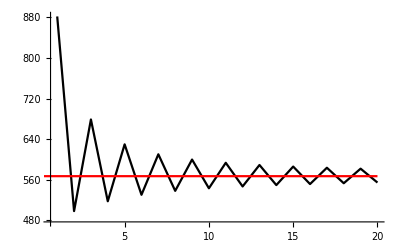

```mathematica
Show[ListLinePlot[EIofN2List,PlotRange->All,PlotStyle->Black],
Plot[EIlimit,{x,0,20},PlotStyle->Red]]
```

```mathematica
Q[1,1]
Q[1,2]
Q[1,3]
Q[1,0]
```

3.17038×10^-10

2.66174×10^-10

3.17038×10^-10

2.66174×10^-10

```mathematica
Dbar[1]
Dbar[3]
Dbar[2]
Dbar[0]
```

{-1.42507×10^10,-3.06911×10^9,-4.67454,-1.79388}

{-1.42507×10^10,-3.06911×10^9,-4.67454,-1.79388}

{1.42507×10^10,3.06911×10^9,4.67454,1.79388}

{1.42507×10^10,3.06911×10^9,4.67454,1.79388}

```mathematica
Eigenvalues[MeMat[1]]
Eigenvalues[Transpose[MeMat[1]]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

{0.911336,-0.911336,-0.564217,0.564217}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

{-0.911336,0.911336,0.564217,-0.564217}

```mathematica
(Inverse[MνMat[1]].DiagonalMatrix[Λ[1]].MνMat[1]-MeMat[1])//Chop
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(Inverse[MνMat[2]].DiagonalMatrix[Λ[2]].MνMat[2]-MeMat[2])//Chop
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{0.541541,-4.02733,0.176236,-1.34966},{3.17038×10^-10,3.74451×10^-10,-1.28756×10^-10,-1.03111×10^-10},{1.54061×10^-10,-1.25174×10^-9,-7.01717×10^-11,3.91878×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}